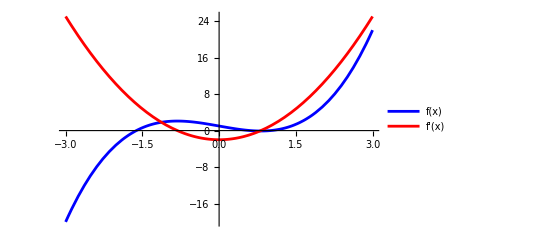

```mathematica
Plot[Evaluate[{x^3-2 x+1,D[x^3-2 x+1,x]}],{x,-3,3},PlotLegends->{"f(x)","f'(x)"},PlotStyle->{Blue,Red}]
```

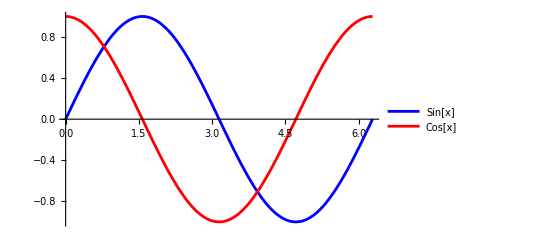

```mathematica
Plot[Evaluate[{Sin[x],D[Sin[x],x]}],{x,0,2 Pi},PlotLegends->{"Sin[x]","Cos[x]"},PlotStyle->{Blue,Red}]
```

```mathematica
r = DSolve[D[y[x],{x,2}]-3 D[y[x],x]+2 y[x]==0,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]}}

```mathematica
r[[1]]/.C[1]->1
```

{y[x]→ⅇ^x+ⅇ^(2 x) C[2]}

```mathematica
sol=DSolve[D[y[x],{x,2}]-3 D[y[x],x]+2 y[x]==0,y,x]
```

{{y→Function[{x},ⅇ^x C[1]+ⅇ^(2 x) C[2]]}}

```mathematica
yFunc[x_]:=y[x]/. sol[[1]]
```

```mathematica
Clear[sol];
sol=DSolve[{D[y[x],x]+y[x]*Tan[x]==Sec[x],y[0]==1},y,x]
```

{{y→Function[{x},Cos[x]+Sin[x]]}}

```mathematica
Clear[sol1];
sol1[x_]=y[x]/.sol[[1]]
```

Cos[x]+Sin[x]

```mathematica
N[sol1[1]]
```

1.38177

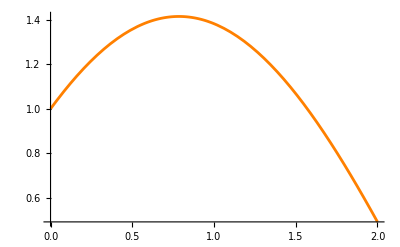

```mathematica
Plot[sol1[x], {x,0,2},PlotStyle->{Red, Green, Orange}]
```

```mathematica
farsol=DSolve[x^2*D[y[x],x]+x*y[x]+1==0,y[x],x]
```

{{y[x]→C[1]/x-Log[x]/x}}

```mathematica
farsol140[x_]=y[x]/.farsol
```

{C[1]/x-Log[x]/x}

```mathematica
D[farsol140[x],{x,5}]
```

{-274/x^6-(120 C[1])/x^6+(120 Log[x])/x^6}

```mathematica
farsol140c1=farsol140[x]/.C[1]->{1,0.5}
```

{{1/x-Log[x]/x,0.5/x-Log[x]/x}}

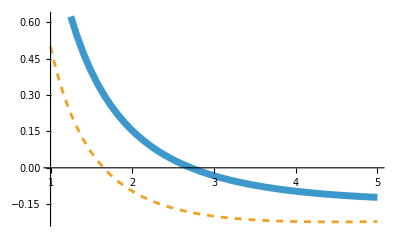

```mathematica
Plot[farsol140c1,{x,1,5}, PlotStyle->{AbsoluteThickness[5],Dashed}]
```

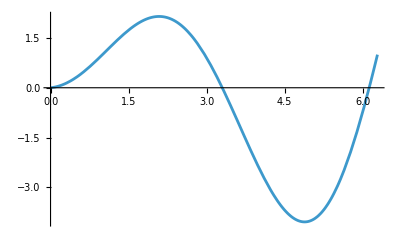

```mathematica
Plot[Evaluate[y[x]/.DSolve[{x*(D[y[x], x]-x*Cos[x])-y[x]==0, y[1]==1},y,x][[1,1]]],{x,0,2*Pi}]
```

```mathematica
DSolve[{x*(D[y[x], x]-x*Cos[x])-y[x]==0, y[1]==1},y,x][[1,1]]
```

y→Function[{x},x-x Sin[1]+x Sin[x]]